# 积分公式的推导和用量傅变换分解HLG模为轨道模

Lawrence Lee

北京理工大学

2020.10.31

用HLG的SU(2)表示表示HG→LG变换。HLG模的含时相干态可化简为高斯波包的闭形式。
用该闭形式推导高斯波包的在椭圆轨道积分以表示分数OAM的轨道模式。一方面，椭圆轨道模式是简并的HLG模式的叠加。用推导的公式和量子傅变换，HLG【逆向地】表示为椭圆轨道模式的叠加。该表示揭示了HLG模式和椭圆轨道丛的关系。

-Graphics-

可能用到的程序包

<< MaTeX`;
<< Notation`;
<< MATLink`;
OpenMATLAB[];
<< GroupTheory`;
<< Quantum`Notation`;
SetQuantumAliases[];

```mathematica
<<MaTeX`
```

## 1. 介绍

HLG模含有点错位和边缘错位。用SU(2)代数，HLG模可被表示为简并的HG模的叠加【计算很困难】。

球腔的近轴波动方程=2D谐振子的薛定谔方程，用激光横模求经典物理中的波函数。椭圆轨道模式：位于椭圆轨道上的模式。位于周期轨道的波动方程与量子线性相关，如，导电性波动

#### HLG模与椭圆轨道模的关系？

椭圆轨道模式=简并的HLG模的叠加

#### 文章结构

HLG模的SU(2)表示表示HG与LG之间的变换

薛定谔相干态公式构建含时HLG基相干态，以验证其可写成闭形式的高斯波包

与HLG模有关的椭圆轨道模写为高斯波包的在轨道上的积分

椭圆轨道模式=简并的HLG模的叠加

用叠加公式和量傅变换可写为HLG模可写为【不同椭偏度和转角】椭圆轨道模的叠加

创新：HLG模写为高斯波包态对的积分，不含HG和LG多项式

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
TeXForm["ε"]
```

\varepsilon

```mathematica
MaTeX["",Magnification->2]//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

## 2. HLG模的SU(2)表示

球腔中横HG模=2D同性阵子的本征函数。

```mathematica
<<Notation`
```

```mathematica
Symbolize[Subscript[a, 1]^†]
Symbolize[Subscript[a, 2]^†]
Symbolize[Subscript[b, 1]^†]
Symbolize[Subscript[b, 2]^†]
Symbolize[Subscript[n, 1]]
Symbolize[Subscript[n, 2]]
Symbolize[Subscript[ψ, Subscript[n, 1],Subscript[n, 2]]^(HG)]
Symbolize[Subscript[ψ, 0,0]]
Symbolize[Subscript[Ψ, Subscript[n, 1],Subscript[n, 2]]^(α,β)]
Symbolize[x̃]
Symbolize[ỹ]
Symbolize[∂/(∂t)]
Symbolize[∂/(∂s)]
Symbolize[Subscript[w, 0]]
Symbolize[Subscript[z, R]]
```

```mathematica
Subscript[ψ, 0,0][t_,s_]:=1/(√π)ⅇ^(-(t+s)^2/2)
SuperDagger[Subscript[a, 1]][t_]:=1/(√2)(t-∂/(∂t))
SuperDagger[Subscript[a, 2]][s_]:=1/(√2)(s-∂/(∂s))
(Subscript[ψ, Subscript[n, 1],Subscript[n, 2]]^(HG))[t_,s_]:=((SuperDagger[Subscript[a, 1]][t])^Subscript[n, 1](SuperDagger[Subscript[a, 2]][s])^Subscript[n, 2])/(√(Subscript[n, 1]!)√(Subscript[n, 2]!))Subscript[ψ, 0,0][t,s]
```

```mathematica
Subscript[n, 1]=Subscript[n, 2]=2;
(Subscript[ψ, Subscript[n, 1],Subscript[n, 2]]^(HG))[t,s]//Simplify
```

(ⅇ^(-1/2 (s+t)^2) (∂/(∂s)-s)^2 (∂/(∂t)-t)^2)/(8 √π)

```mathematica
D[#, s]&
```

```mathematica
(∂/(∂s)-s)^2 (∂/(∂t)-t)^2//Expand
```

(∂/(∂s))^2 (∂/(∂t))^2 s^2-2 (∂/(∂s))^2 ∂/(∂t) s^2 t+(∂/(∂s))^2 s^2 t^2

```mathematica
D[s^2,{t,2},{s,2}]+D[2 s^2 t,{t,1},{s,2}]+D[t^2 s^2,{s,2}]
```

4+2 t^2

```mathematica
(Subscript[ψ, Subscript[n, 1],Subscript[n, 2]]^(HG))[t_,w_]:=(ⅇ^(-1/2 (t+w)^2) (4+2 t^2))/(8 √π)
```

带入下式

```mathematica
w[z_]:=Subscript[w, 0] √(1+(z/Subscript[z, R])^2)
x̃[x_]:=(√2 x)/w[z]
ỹ[y_]:=(√2 y)/w[z]
```

```mathematica
Subscript[w, 0]=.
Subscript[z, R]=.
```

```mathematica
(Subscript[ψ, Subscript[n, 1],Subscript[n, 2]]^(HG))[x̃[x],ỹ[y]]//FullSimplify
```

(ⅇ^(-((x+y)^2 z_R^2)/(w_0^2 (z^2+z_R^2))) (x^2 z_R^2+w_0^2 (z^2+z_R^2)))/(2 √π w_0^2 (z^2+z_R^2))

General::munfl: Exp[-1.59994×10^11] is too small to represent as a normalized machine number; precision may be lost.

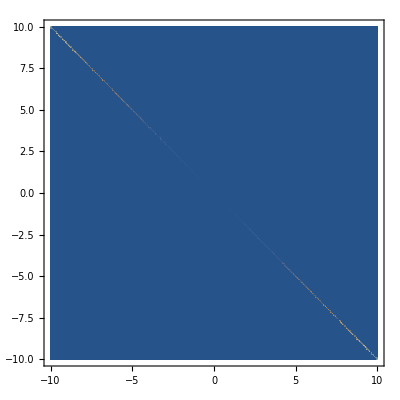

```mathematica
λ=1050*10^-9;
Subscript[w, 0]=5*10^-5;
Subscript[z, R]=π Subscript[w, 0]^2/λ;
z=0;
DensityPlot[(ⅇ^(-((x+y)^2 Subscript[z, R]^2)/(Subscript[w, 0]^2 (z^2+Subscript[z, R]^2))) (x^2 Subscript[z, R]^2+Subscript[w, 0]^2 (z^2+Subscript[z, R]^2)))/(2 √π Subscript[w, 0]^2 (z^2+Subscript[z, R]^2)),{x,-10,10},{y,-10,10},PlotPoints->100]
```

```mathematica
Plot[(2^(1/2 (-Subscript[n, 1]-Subscript[n, 2])) ⅇ^(-(π (x+y)^2 Subscript[z, R])/((z^2+Subscript[z, R]^2) λ)) (-∂/(∂t)+(√(2 π) x)/(√(1+z^2/Subscript[z, R]^2) √(Subscript[z, R] λ)))^Subscript[n, 1] (-∂/(∂w)+(√(2 π) y)/(√(1+z^2/Subscript[z, R]^2) √(Subscript[z, R] λ)))^Subscript[n, 2])/(√π √(Subscript[n, 1]!) √(Subscript[n, 2]!)),{x,-10,10},{y,-10,10}]
```

用SU(2)代数，HLG模可连续从HG变到LG模，推广式为

```mathematica
(Subscript[Ψ, Subscript[n, 1],Subscript[n, 2]]^(α,β))[t_,w_]:=((SuperDagger[Subscript[b, 1]][t])^Subscript[n, 1](SuperDagger[Subscript[b, 2]][w])^Subscript[n, 2])/(√(Subscript[n, 1]!)√(Subscript[n, 2]!))Subscript[ψ, 0,0][t,w]
```

其中

```mathematica
({{SuperDagger[Subscript[b, 1]]}, {SuperDagger[Subscript[b, 2]]}})=({{ⅇ^(-ⅈ α/2)Cos[β/2], ⅇ^(ⅈ α/2)Sin[β/2]}, {-ⅇ^(-ⅈ α/2)Sin[β/2], ⅇ^(ⅈ α/2)Cos[β/2]}}).({{SuperDagger[Subscript[a, 1]]}, {SuperDagger[Subscript[a, 2]]}});
```

```mathematica
α=.
β=.
SuperDagger[Subscript[b, 1]]
SuperDagger[Subscript[b, 2]]
```

a_1^† ⅇ^(-(ⅈ α)/2) Cos[β/2]+a_2^† ⅇ^((ⅈ α)/2) Sin[β/2]

a_2^† ⅇ^((ⅈ α)/2) Cos[β/2]-a_1^† ⅇ^(-(ⅈ α)/2) Sin[β/2]

```mathematica
α=π/2;
β=π/2;
SuperDagger[Subscript[b, 1]]
SuperDagger[Subscript[b, 2]]
```

(a_1^† ⅇ^(-(ⅈ π)/4))/(√2)+(a_2^† ⅇ^((ⅈ π)/4))/(√2)

-(a_1^† ⅇ^(-(ⅈ π)/4))/(√2)+(a_2^† ⅇ^((ⅈ π)/4))/(√2)

则Ψ_(n_1,n_2)^(0,0)[t,w]=ψ_(n_1,n_2)^(HG)[t,w]，则Ψ_(n_1,n_2)^(π/2,π/2)[t,w]=ψ_(n_1,n_2)^(LG)[t,w]

注：LG的角量子数为l=n_2-n_1，径向量子数p=Min[n_1,n_2]

n_1=4,n_2=3，改变α∈[0,π/2]和β∈[0,π/2]

光子的拓扑荷

```mathematica
OAM[α_,β_]:=ℏ(Subscript[n, 1]-Subscript[n, 2])Sin[α]Sin[β]
```

HG/LG的拓扑荷

```mathematica
OAM[0,0]
OAM[π/2,π/2]
```

0

ℏ (n_1-n_2)

-Graphics-

### 2.1

### 2.2

### 2.3

### 2.4

-Graphics-中心沿椭圆轨道运动的高斯波包

-Graphics-椭圆轨道模=高斯波包沿沿椭圆轨道的积分

-Graphics- HLG模=不同相位因子ϕ椭圆轨道模的叠加

波包=波函数的叠加=本征态的加权求和，但若求和的结果形如“山丘”，则说是波包

```mathematica
Rasterize[-Graphics-,RasterSize->1000]//Print
```

```mathematica
TeXForm["ε"]
```

\varepsilon

```mathematica
MaTeX["",Magnification->2]//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

## 3. 椭圆轨道模式

猜：椭圆轨道模式，可能是LG模

薛定谔用H多项式的生成方程推导出高斯波包

```mathematica
GeneratingFunction[HermiteH[m,x],n,x]
```

HermiteH[m,x]/(1-x)

```mathematica
GeneratingFunction[HermiteH[3,x],n,x]
```

(-12 x+8 x^3)/(1-x)

```mathematica
∑_(n=0)^∞ u^n/(√(n!))ⅇ^(-(Abs[u])^2/2)1/(√(2^n n!))HermiteH[n,x] ⅇ^(-x^2/2)
=ⅇ^(-x^2/2-Abs[u]^2/2)∑_(n=0)^∞ u^n/(n!)HermiteH[n,x]/(√(2^n))
=ⅇ^(-x^2/2-Abs[u]^2/2)ⅇ^(√2 ux-u^2/2)
```

```mathematica
ⅇ^(-x^2/2-Abs[u]^2/2)ⅇ^(√2 u x-u^2/2)/.u->√M ⅇ^(-ⅈ(ω t+ϕ))
```

ⅇ^(-1/2 ⅇ^(-2 ⅈ (ϕ+t ω)) M+√2 ⅇ^(-ⅈ (ϕ+t ω)) √M x-x^2/2-1/2 ⅇ^(2 Im[ϕ+t ω]) Abs[M])

高斯波包的中央峰同经典运动

```mathematica
u=√M ⅇ^(-ⅈ(ω t+ϕ));
x̃=√2 Re[u]
```

√2 Re[ⅇ^(-ⅈ (ϕ+t ω)) √M]

相位因子ϕ与初位置有关。使用薛定谔相干态表示，HLG为基的相干态可被表示为

```mathematica
g^(α,β)(x̃,ỹ,Subscript[u, 1],Subscript[u, 2])==∑_(Subscript[n, 1]=0)^∞ ∑_(Subscript[n, 2]=0)^∞ Subscript[u, 1]^Subscript[n, 1]/(√(Subscript[n, 1]!))Subscript[u, 2]^Subscript[n, 2]/(√(Subscript[n, 2]!))e^(-(Abs[Subscript[u, 1]]^2+Abs[Subscript[u, 2]]^2)/2)Subscript[Ψ, Subscript[n, 1],Subscript[n, 2]]^(α,β)(x̃,ỹ)
```

其中

```mathematica
[{{Subscript[u, 1]}, {Subscript[u, 2]}}]==[{{√Subscript[N, 1] e^(-i(θ+ϕ/2))}, {√Subscript[N, 2] e^(-i(θ-ϕ/2))}}]
```

变量θ表示ωt∈[0,2π]，N_1N_2与椭圆轨道有关。则波包态g^(α,β)(x̃,ỹ,u_1,u_2)可写为闭形式

```mathematica
g^(α,β)(x̃,ỹ,Subscript[u, 1],Subscript[u, 2])==∑_(Subscript[n, 1]=0)^∞ ∑_(Subscript[n, 2]=0)^∞ Subscript[N, 1]^(Subscript[n, 1]/2)/(√(Subscript[n, 1]!))Subscript[N, 2]^(Subscript[n, 2]/2)/(√(Subscript[n, 2]!))e^(-(Subscript[N, 1]+Subscript[N, 2])/2)Subscript[Ψ, Subscript[n, 1],Subscript[n, 2]]^(α,β)(x̃,ỹ)e^(-i(Subscript[n, 1]+Subscript[n, 2])θ)e^(-i(Subscript[n, 1]-Subscript[n, 2])ϕ/2)
```

g^(α,β)(x̃,ỹ,u_1,u_2)也可写为【5式和8式】

```mathematica
g^(α,β)(x̃,ỹ,Subscript[u, 1],Subscript[u, 2])==1/(√π)e^(-((x̃)^2-2 √2 Subscript[v, 1] x̃+Subscript[v, 1]^2+Abs[Subscript[v, 1]]^2)/2)e^(-((ỹ)^2-2 √2 Subscript[v, 2] ỹ+Subscript[v, 2]^2+Abs[Subscript[v, 2]]^2)/2)
```

其中

```mathematica
[{{Subscript[v, 1]}, {Subscript[v, 2]}}]==[{{e^(-iα/2)cos(β/2), -e^(-iα/2)sin(β/2)}, {e^(iα/2)sin(β/2), e^(iα/2)cos(β/2)}}][{{Subscript[u, 1]}, {Subscript[u, 2]}}]
```

6式和13式，写为含a_1^†和a_2^†的形式

```mathematica
g^(α,β)(x̃,ỹ,Subscript[u, 1],Subscript[u, 2])==∑_(Subscript[m, 1]=0)^∞ ∑_(Subscript[m, 2]=0)^∞ Subscript[v, 1]^Subscript[m, 1]/(Subscript[m, 1]!)Subscript[v, 2]^Subscript[m, 2]/(Subscript[m, 2]!)e^(-(Abs[Subscript[v, 1]]^2+Abs[Subscript[v, 2]]^2)/2)(SuperDagger[Subscript[a, 1]])^Subscript[m, 1](SuperDagger[Subscript[a, 2]])^Subscript[m, 2] Subscript[ψ, 0,0](x̃,ỹ)
```

用θ==ωt，g^(α,β)(x̃,ỹ,u_1,u_2)为高斯波包，中央峰沿椭圆轨道x̃==√2 Re(v_1) and ỹ==√2 Re(v_2)，静态椭圆模为

```mathematica
Subscript[Φ, Subscript[N, 1],Subscript[N, 2]]^(α,β)(x̃,ỹ,ϕ)==1/(2π)∫_0^(2π) g^(α,β)(x̃,ỹ,Subscript[u, 1],Subscript[u, 2])e^(i(Subscript[N, 1]+Subscript[N, 2])θ)dθ
```

10表明，高斯波包g^(α,β)(x̃,ỹ,u_1,u_2)是HLG模Ψ_(n_1,n_2)^(α,β)(x̃,ỹ)的叠加

```mathematica
1/(2π)∫_0^(2π) e^(i(n-n')θ)dθ==Subscript[δ, n,n']
```

静态相干态可写为

```mathematica
{{Subscript[Φ, Subscript[N, 1],Subscript[N, 2]]^(α,β)(x̃,ỹ,ϕ), ==1/(2π)∫_0^(2π) 1/(√π)e^(-((x̃)^2-2 √2 Subscript[v, 1] x̃+Subscript[v, 1]^2+Abs[Subscript[v, 1]]^2)/2)e^(-((ỹ)^2-2 √2 Subscript[v, 2] ỹ+Subscript[v, 2]^2+Abs[Subscript[v, 2]]^2)/2)e^(i(Subscript[N, 1]+Subscript[N, 2])θ)dθ}, {, ==∑_(K==-Subscript[N, 2])^Subscript[N, 1] Subscript[N, 1]^((Subscript[N, 1]-K)/2)/(√((Subscript[N, 1]-K)!))Subscript[N, 2]^((Subscript[N, 2]+K)/2)/(√((Subscript[N, 2]+K)!))e^(-(Subscript[N, 1]+Subscript[N, 2])/2)e^(-i(Subscript[N, 1]-Subscript[N, 2])ϕ/2)Subscript[Ψ, Subscript[N, 1]-K,Subscript[N, 2]+K]^(α,β)(x̃,ỹ)e^iKϕ}}
```

其中Ψ_(N_1-K,N_2+K)^(α,β)(x̃,ỹ)，n_1+n_2==N_1+N_2被重新分组，用新的指数K表示n_1==N_1-K，n_2==N_2-K的叠加模式。对于(N_1,N_2,ϕ)和(α,β)，模式Φ_(N_1,N_2)^(α,β)(x̃,ỹ,ϕ)的空间强度集中在椭圆轨道上，椭圆轨道模式Φ_(N_1,N_2)^(α,β)(x̃,ỹ,ϕ)的OAM为

```mathematica
<Subscript[L, z]≥ℏ(Subscript[n, 1]-Subscript[n, 2])Sin[α]Cos[β]+2 √(Subscript[n, 1] Subscript[n, 2])(Cos[α]Sin[ϕ]+Cos[β]Sin[α]Cos[ϕ])
```

### 3.1

### 3.2

### 3.3

### 3.4

```mathematica
Rasterize[,RasterSize->1000]//Print
```

```mathematica
TeXForm["ε"]
```

\varepsilon

```mathematica
MaTeX["",Magnification->2]//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

## 4. 离散傅变换

Ψ_(N_1,N_2)^(α,β)(x̃,ỹ)==[N_1^(N_1/2)/(√(N_1!))N_2^(N_2/2)/(√(N_2!))e^(-N/2)]^-1 1/(N+1)∑_(n=0)^N Φ_(N_1,N_2)^(α,β)(x̃,ỹ,ϕ_n)e^(i(N_1-N_2)ϕ_n/2)

HLG模可写为广义椭圆模式【高斯波包套沿轨道的积分】的叠加

### 4.1 Φ_(N_1,N_2)^(0,0)(x̃,ỹ,ϕ_n)

Ψ_(N_1,N_2)^(0,0)(x̃,ỹ)为HG模ψ_(N_1,N_2)^(HG)(x̃,ỹ)

椭圆轨道模Φ_(7,8)^(0,0)(x̃,ỹ,n π/8) n=0,1…5

椭圆度 & 主轴方向

-Graphics-

### 4.2

-Graphics-

### 4.3

-Graphics-

### 4.4

```mathematica
Rasterize[-Graphics-,RasterSize->1000]//Print
```

-Graphics-

```mathematica
TeXForm["ε"]
```

\varepsilon

```mathematica
MaTeX["",Magnification->2]//Print
```

```mathematica
MaTeX["\\begin{aligned}
&=\\\\
&=\\\\
\\end{aligned}",Magnification->2]//Print
```

## 5. 总结

1. 推导出了含时HLG基相干态的高斯波包的闭形式

2. 用该闭形式推导椭圆轨道模式【=高斯波包态沿轨道的积分】

3. 椭圆轨道模式是简并的HLG模式的叠加

4. 用推导出来的公式和量子傅里叶变换证明：HLG模可逆向表示为椭圆轨道模式的叠加

5. HLG模的完整形式可清楚地表示量子-经典对应关系